# Mathematica Research Project

### Kevin O' Sullivan -Graphics-

## Project Introduction

Please note that due to re sampling / sub sampling of the original dataset which is too large for my computer, there may be inconsistencies in some of the output cells and the descriptions.

The main focus of this project is to implement various pieces of the mathematica toolset, in particular some of the parts of mathematica covered in the ACM40730 module “Introduction to Mathematica”. The primary goal of the project is to develop a mortality predictor for individuals who have been infected by the viral infection Covid-19. This viral infection has taken the world by surprise and put pressure on medical resources. For this reason it is important that a hospital or any medical resource provision centre would be able to classify incoming patients in terms of their likelihood of death. This can allow for the most vulnerable patients to receive the attention and resources they get. This concept is known as a triage which is defined by Wikipedia to be :

“Triage is the process of determining the priority of patients’ treatments by the severity of their condition or likelihood of recovery with and without treatment.”

There are a number of sections in this project and they are outlined as follows :

1.  Dataset Description
2.  Data pre processing
3.  Exploratory Data Analysis
4.  Model Training and Evaluation
5.  Visualisations
6.  Conclusions

## Dataset Description

The dataset is available in a github repository here : https://github.com/beoutbreakprepared/nCoV2019
The dataset is described in detail in this research paper: https://rdcu.be/cbZzD

The dataset was curated by a group of researchers Xu, B., Gutierrez, B., Mekaru, S. et al.. It is a conglomerate of datasets 
which were made available by government bodies and various groups. Patient level covid 19 data is very limited at this point in time,
with most current covid-19 data being used for aggregated analysis such as cases per region.  This dataset contains 26 million records.
Many of the columns however only have a very small few consistent entries making them not appropriate for model training.

## Data Pre-Processing

#### Data Import

```mathematica
file=Import["/Users/kevinosullivan/Desktop/Masters/Semester 1/Mathematica/Covid-19/sub.csv"];
headers=file[[1]];
data=file[[2;;]];
```

```mathematica
testset=Thread[headers->#]&/@data//Map[Association]// Dataset;
```

The data set has been imported. The dataset has approximately 2.6 million records. The columns in the data are :

```mathematica
testset[1,Keys]
```

#### Data Selection

The dataset contains a large number columns, however , many of the columns will not be needed for this project. The columns
 needed for this project will be any values that could be useful for mortality prediction as well as some columns for some 
 exploratory  analysis and visualisations. 

Many of the columns have very few values eg. chronic_disease has only 143 examples with values in the 2.6 million patients. 
While this would be useful information there is very limited data here to train a model. For this reason the variables used in 
the model are limited. A model will be trained with only the variables age, sex, chronic_disease_binary and outcome as the 
dependent variable which are the variables with the most consistent examples and have a sample of 33,539 patients. There 
is very limited availability of patient level covid 19 data at this point.

Number of values for chronic_disease in dataset :

```mathematica
Length[testset[Select[#"chronic_disease" ≠ "" &]]]
```

138

The variables in the dataset I will be using for the mortality prediction model are :

age :  the age of the patient

sex :  the sex of the patient

chronic_disease_binary : a binary variable describing whether a patient has a chronic disease or not

outcome : describes the outcome of the patient eg.recovered

```mathematica
modelData = testset[Select[NumericQ[#age] && #sex≠""&& #"chronic_disease_binary"≠""&& #"outcome"≠""&],{"age","sex","chronic_disease_binary","outcome"}]
```

Dataset[<>]

#### Data Manipulation & Pre Processing

Some of the columns contain categorical variables and these will have to be split into levels and represented by binary variables.

Convert variable sex to binary representation ( 0 = female | 1 = male )

```mathematica
modelData = modelData[All,If[#"sex"=="male",<|#,"sex"->1|>,<|#,"sex"->0|>]&];
```

Convert variable chronic_disease_binary to binary representation ( 0 = No Chronic Disease | 1 = Chronic Disease )

```mathematica
modelData = modelData[All,If[#"chronic_disease_binary"=="True",<|#,"chronic_disease_binary"->1|>,<|#,"chronic_disease_binary"->0|>]&];
```

Convert the values of outcome column to either 1 ( Dead ) or 0 ( Recovered ). Some values in this column are not useful here such as “hospitalised” or “critical condition”. 
Thees are not potential outcomes that our classifier will consider as we are predicting mortality, which is a binary value.

```mathematica
modelData = modelData[All,If[#"outcome"=="death" || #"outcome"=="Dead" || #"outcome"=="Death" || #"outcome"=="Died" || #"outcome"=="dead"|| #"outcome"=="died" || #"outcome"=="Deceased",<|#,"outcome"->1|>,<|#,"outcome"->#outcome|>]&];
modelData = modelData[All,If[#"outcome"=="discharge" ||#"outcome"=="discharged" || #"outcome"=="Discharged" || #"outcome"=="recovered" || #"outcome"=="Alive" || #"outcome"=="Recovered",<|#,"outcome"->0|>,<|#,"outcome"->#outcome|>]&];
modelData = modelData[Select[#outcome==0 || #outcome==1&],All];
```

## Exploratory Data Analysis

In this section I will explore the data. I will look at the distributions of the different variables and also the relationships between the relevant variables.

#### Age

Histogram of age:

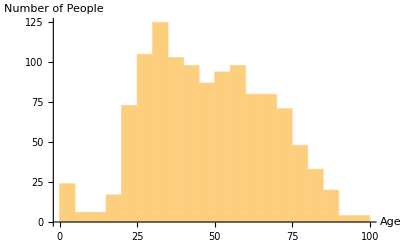
-Graphics-Histogram of Age

```mathematica
Labeled[Histogram[modelData[All,"age"],AxesLabel->{"Age","Number of People"}],"Histogram of Age"]
```

This shows the distribution of the age variable. There are very few young people in this dataset, The age groups of 0-5, 5-10, 10-15 and15-20 years old all have few examples in the dataset. 
Most of the dataset is between 20 and 80 years old. There are very few examples older than 80 also. This is to be expected. The 30-35 years old bar is highest and this agegroup has more indiviuals than any other agegroup.

```mathematica
Median[modelData[All,"age"]]
```

46

```mathematica
Mean[modelData[All,"age"]]
```

47.341

The median value for age is 46 and the mean is very similar at 47.0782.

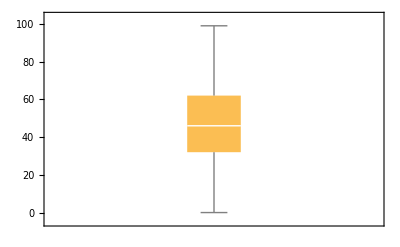
-Graphics-Age Boxplot

```mathematica
Labeled[BoxWhiskerChart[modelData[All,"age"]],"Age Boxplot"]
```

The box plot shows the distribution of the age variable. The interquartile range goes from 32 to 61. So 25% of the dat has age below 32 and 75% has age below 61.

#### Sex

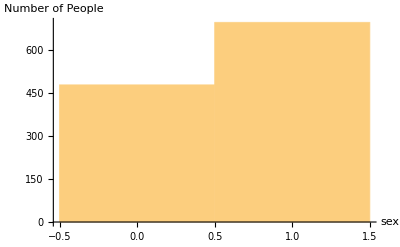
-Graphics-Histogram of Sex

```mathematica
Labeled[Histogram[modelData[All,"sex"],AxesLabel->{"sex","Number of People"}],"Histogram of Sex"]
```

The histogram shows the two groups 0 = female and 1 = male . There are slightly more males than females in the dataset.

```mathematica
Labeled[GroupBy[modelData,"sex",Length],"Frequency Table for sex"]
```

Frequency Table for sex

There are 2912 males and 2491 females in the dataset.

#### Chronic Disease Binary

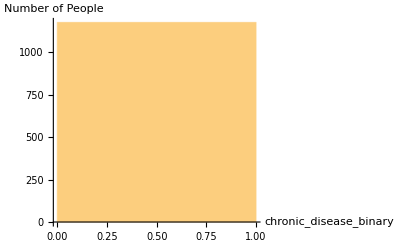
-Graphics-Histogram of Chronic Disease Binary

```mathematica
Labeled[Histogram[modelData[All,"chronic_disease_binary"],AxesLabel->{"chronic_disease_binary","Number of People"}],"Histogram of Chronic Disease Binary"]
```

Group with chronic_disease_binary=0 do not have a chronic disease, they make up almost all of the dataset. About 5100 of the people have no chronic disease. A small percentage of the data has a chronic disease, about 100 people.

```mathematica
Labeled[GroupBy[modelData,"chronic_disease_binary",Length],"Frequency Table for chronic disease binary"]
```

Frequency Table for chronic disease binary

121 of the patients have a chronic disease and 5282 do not.

#### Outcome

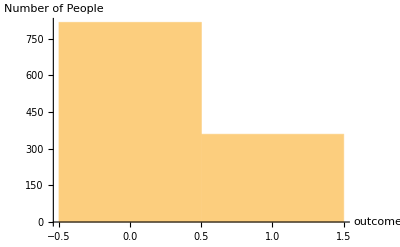
-Graphics-Histogram of Outcome

```mathematica
Labeled[Histogram[modelData[All,"outcome"],AxesLabel->{"outcome","Number of People"}],"Histogram of Outcome"]
```

The histogram shows that significantly more people survived than died.

```mathematica
Labeled[GroupBy[modelData,"outcome",Length],"Frequency Table for outcome"]
```

Frequency Table for outcome

#### Age Vs Outcome

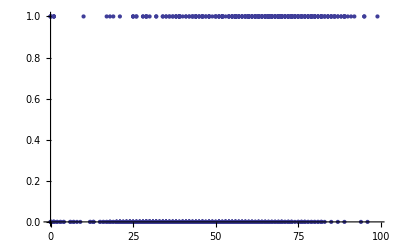

```mathematica
ListPlot[Transpose[{Normal[modelData[All,"age"]],Normal[modelData[All,"outcome"]]}],PlotTheme->"Classic"]
```

The scatterplot of age vs outcome shows two distinct lines of dots. One line is at outcome = 0 this is the group that survived. The group at outcome = 1 is the group that died. 
The group with outcome = 0 seems to be more concentrated to the left than the group outcome = 1. This would suggest a lower expected age in survivors. I will
investigate this with some descriptive statistics in particular the mean and median. These are both measures of centre.

```mathematica
Median[modelData[Select[#"outcome"==1 &], "age"]]
```

65

```mathematica
Median[modelData[Select[#"outcome"==0 &], "age"]]
```

39

```mathematica
40
```

40

As expected, the median of the group that died is 64 and is significantly higher than the group that survived, whose average age is 40 years old.

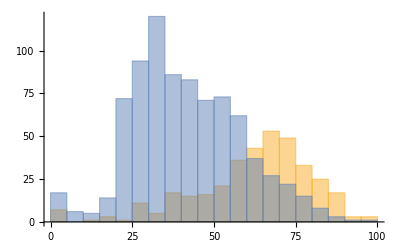

```mathematica
Histogram[{Normal@modelData[Select[#"outcome"==1&],"age"],Normal@modelData[Select[#"outcome"==0&],"age"]}]
```

The group that died is plotted in orange. It is much smaller and its median value is much higher than the group that recovered. The 
group that died is significantly older on average and most of its data is distributed between 40 and 80 years old.

```mathematica
N[Mean[modelData[Select[#"outcome"==1 &], "age"]]]
```

61.493

```mathematica
N[Mean[modelData[Select[#"outcome"==0 &], "age"]]]
```

41.1224

Similarly, the mean of the group that died is 61.77, and the mean of the group that recovered is 42.3.

#### Sex Vs Outcome

```mathematica
PairedHistogram[Normal@modelData[Select[#"outcome"==1&],"sex"],Normal@modelData[Select[#"outcome"==0&],"sex"],ChartLabels->{"died","recovered"}]
```

-Graphics-

The group with that recovered has almost equal males and females. The group that died has significantly more males than females

```mathematica
GroupBy[modelData[Select[#"outcome"==1&],All],"sex",Length]
```

```mathematica
GroupBy[modelData[Select[#"outcome"==1&],All],"chronic_disease_binary",Length]
```

There are 841 males that died and only 483 females.

#### Chronic Disease Binary Vs Outcome

```mathematica
PieChart[{{Length[modelData[Select[#"outcome"==1&& #"chronic_disease_binary"==1&],"chronic_disease_binary"]],Length[modelData[Select[#"outcome"== 1&& #"chronic_disease_binary"==0&],"chronic_disease_binary"]]},{Length[modelData[Select[#"outcome"==0&& #"chronic_disease_binary"==1&],"chronic_disease_binary"]],Length[modelData[Select[#"outcome"== 0&& #"chronic_disease_binary"==0&],"chronic_disease_binary"]]}},ChartLabels->{"Chronic Disease","None"}]
```

-Graphics-

This donut chart shows the portion of each group that had chronic disease. The central pie chart has the group that died, there 
is a significant portion of the group that has a chronic disease. In the group that recovered it is a very small percentage.

```mathematica
Labeled[PercentForm[N[Length[modelData[Select[#"outcome"==1&& #"chronic_disease_binary"==1&],"chronic_disease_binary"]]/Length[modelData[All,"chronic_disease_binary"]]]],"Percentage of chronic disease in Died",Top]
```

0%Percentage of chronic disease in Died

```mathematica
Labeled[PercentForm[N[Length[modelData[Select[#"outcome"==0&& #"chronic_disease_binary"==1&],"chronic_disease_binary"]]/Length[modelData[All,"chronic_disease_binary"]]]],"Percentage of chronic disease in Recovered",Top]
```

0%Percentage of chronic disease in Recovered

There is 1.869% rate of chronic disease in those that died. There is only 0.3702% in those that recovered.This indicates there is a relationship between the variables.

## Model Training and Evaluation

In this section I will train and evaluate a number of models in order to assess which model is the most appropriate. 
The models that will be trained and evaluated are : Nearest Neighbour, Logistic Regression, and an Artificial Neural Network

First give each row in the data a unique ID :

```mathematica
modelData=modelData[AssociationThread[Range@Length@#,#]&];
```

In the model, the predictor variables are age, sex and chronic_disease_binary. These will be the features for the machine learning model. The dependent variable is outcome.
The KeyDrop function is used here which drops all elements with this key, in this case outcome, so the other keys are used.

```mathematica
featSplit=modelData[All,<|"Features"->Values@*KeyDrop["outcome"],"Objective"->Key["outcome"]|>];
```

I will use an 80/20 split for my training and test data . this means 4322 will be in the training set and 1081 for testing.

```mathematica
splitNum=Round[modelData[Length]0.2];
ids=Range@modelData[Length];
testIds=ids~RandomSample~splitNum;
trainIds=ids~Complement~testIds;
tt=featSplit[<|"Test"->testIds,"Train"->trainIds|>];
trainData=tt["Train"];
testData=tt["Test"];
```

### Nearest Neighbour

The Nearest Neighbours algorithm is used for classification and regression. When classifying it assigns the average value of the k nearest neighbours of the data.

#### Train the model

```mathematica
knnFun =Classify[Values[trainData,#Features&]->Values[trainData,#Objective&],Method->"NearestNeighbors"];
```

```mathematica
Information[knnFun,"MethodDescription"]
```

The nearest neighbors classifier infers the class of a new example by analyzing its nearest neighbors in the feature space. In its simplest form, it picks the commonest class amongst the "k"-nearest neighbors.

Append Test Classifications

Now I will use the trained model to classify the test set, and append the classification results as a new column .

```mathematica
featSplit=tt[{"Test"->Query[All,Append[#,<|"Classified as"->knnFun@#Features|>]&]}];
```

Now each example contains:

```mathematica
featSplit["Test",5]
```

#### Classifier Evaluation

```mathematica
ClassifierInformation[knnFun]
```

ClassifierInformation::mlobs: ClassifierInformation is obsolete. It has been superseeded by Information since version 12.

Classifier information
Data type | {Numerical,Boolean,Numerical}
Classes | ,,01
Accuracy | (79.32.4) %
Method | NearestNeighbors
Single evaluation time | 2.41 ms/example
Batch evaluation speed | 57.4 examples/ms
Loss | 0.5 ± 0.038
Model memory | 158. kB
Training examples used | 941 examples
Training time | 567. ms
 |

The model used 4322 examples which is 80% of the data for training. The data types of the model features are
 Numerical, Boolean, Boolean. Age is numerical and sex and chronic disease binary are booleans.

In order to evaluate the model I will create a classifier measurements object and access a number of the available classifier measurements.

The classifier measurements I will use here are :

Accuracy : The classification accuracy of the classifier. This is the fraction of classifications which are correct.

Error : The error rate of the classifier. Accuracy + Error = 1.

Precision : This is the proportion of positive classifications which are correct.

Recall : This is the true positive rate.

F1 Score : provides an average measure of recall and precision. A measure of models accuracy.

```mathematica
measurementsKNN=ClassifierMeasurements[knnFun,Values[testData,#Features&]->Values[testData,#Objective&]];
knnRes =Labeled[TextGrid[{{"Accuracy","Error","Precision","Recall","F1Score"},{ measurementsKNN["Accuracy"], measurementsKNN["Error"], measurementsKNN["Precision"], measurementsKNN["Recall"], measurementsKNN["F1Score"]}},Frame->All],"Nearest Neighbour Classifier Measures",Top]
```

Accuracy | Error | Precision | Recall | F1Score
0.778723 | 0.221277 | <|0→0.809249,1→0.693548|> | <|0→0.880503,1→0.565789|> | <|0→0.843373,1→0.623188|>Nearest Neighbour Classifier Measures

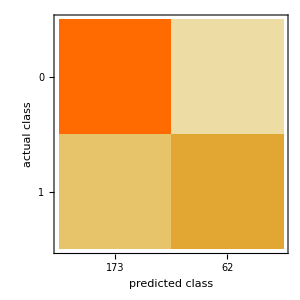
Classifier Measurements
Number of test examples | 235
Accuracy | (77.92.7) %
Accuracy baseline | (67.73.1) %
Geometric mean of probabilities | 0.629 ± 0.022
Mean cross entropy | 0.463 ± 0.034
Single evaluation time | 2.69 ms/example
Batch evaluation speed | 33.7 examples/ms
Rejection rate | 0 %
-Graphics- |

```mathematica
measurementsKNN["Report"]
```

The confusion matrix shows that 168 of the 271 examples which were of class 1 were predicted as class 0. This might be due to the fact there there is a large imbalance in the data and not many examples of class 1.

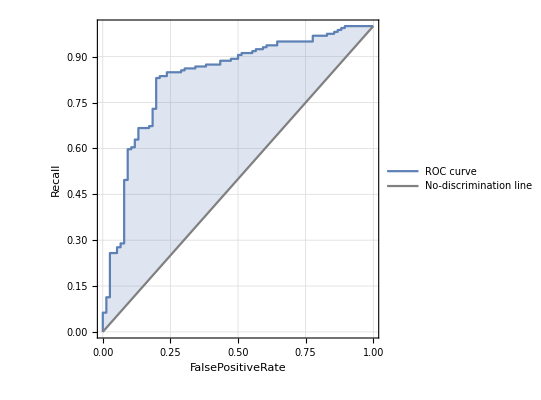
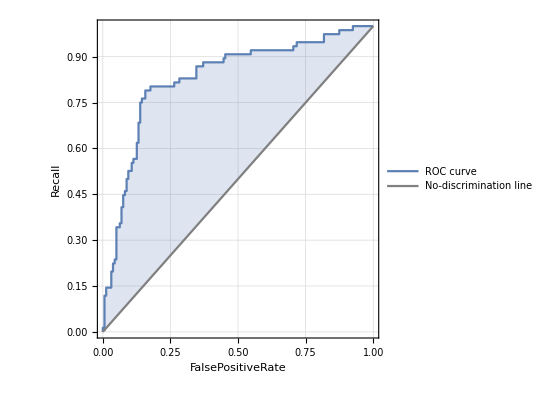
<|0→-Graphics-,1→-Graphics-|>

```mathematica
measurementsKNN["ROCCurve"]
```

The ROC curve for both classes are strongly up to the top left which indicates good performance. The diagonal line at 45 degrees represent a randomised classification.

### Logistic Regression

Logistic regression is a statistical model that uses a logistic function to model a binary dependent variable. Here I will train a logistic regression model and assess its performance

#### Train the model

```mathematica
lrFun =Classify[Values[trainData,#Features&]->Values[trainData,#Objective&],Method->"LogisticRegression"];
```

```mathematica
Information[lrFun,"MethodDescription"]
```

The logistic regression classifier models class probabilities with logistic functions of linear combinations of features. It is also called log-linear model, softmax regression, or maximum-entropy classifier.

```mathematica
Append Test Classifications
```

Append Classifications Test

Now I will use the trained model to classify the test set, and append the classification results as a new column .

```mathematica
featSplit=tt[{"Test"->Query[All,Append[#,<|"Classified as"->lrFun@#Features|>]&]}];
```

Now each example contains:

```mathematica
featSplit["Test",5]
```

#### Classifier Evaluation

```mathematica
ClassifierInformation[lrFun]
```

Classifier information
Data type | {Numerical,Boolean,Numerical}
Classes | ,,01
Accuracy | (79.82.8) %
Method | LogisticRegression
Single evaluation time | 2.14 ms/example
Batch evaluation speed | 176. examples/ms
Loss | 0.501 ± 0.033
Model memory | 258. kB
Training examples used | 941 examples
Training time | 1.42 s
 |

The model used 4322 examples which is 80% of the data for training. The data types of the model features are
 Numerical, Boolean, Boolean. Age is numerical and sex and chronic disease binary are booleans.

In order to evaluate the model I will create a classifier measurements object and access a number of the available classifier measurements.

The classifier measurements I will use here are :

Accuracy : The classification accuracy of the classifier. This is the fraction of classifications which are correct.

Error : The error rate of the classifier. Accuracy + Error = 1.

Precision : This is the proportion of positive classifications which are correct.

Recall : This is the true positive rate.

F1 Score : provides an average measure of recall and precision. A measure of models accuracy.

```mathematica
measurementslr=ClassifierMeasurements[lrFun,Values[testData,#Features&]->Values[testData,#Objective&]];
lrRes = Labeled[TextGrid[{{"Accuracy","Error","Precision","Recall","F1Score"},{ measurementslr["Accuracy"], measurementslr["Error"], measurementslr["Precision"], measurementslr["Recall"], measurementslr["F1Score"]}},Frame->All],"Logistic Regression Measures",Top]
```

Accuracy | Error | Precision | Recall | F1Score
0.782979 | 0.217021 | <|0→0.803371,1→0.719298|> | <|0→0.899371,1→0.539474|> | <|0→0.848665,1→0.616541|>Logistic Regression Measures

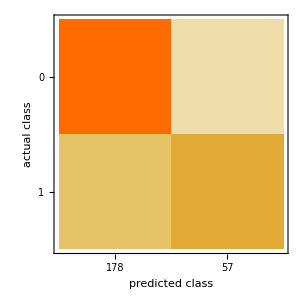
Classifier Measurements
Number of test examples | 235
Accuracy | (78.32.7) %
Accuracy baseline | (67.73.1) %
Geometric mean of probabilities | 0.614 ± 0.022
Mean cross entropy | 0.488 ± 0.036
Single evaluation time | 2.36 ms/example
Batch evaluation speed | 87.7 examples/ms
Rejection rate | 0 %
-Graphics- |

```mathematica
measurementslr["Report"]
```

The confusion matrix shows that 189 of the 289 examples which were of class 1 were predicted as class 0.

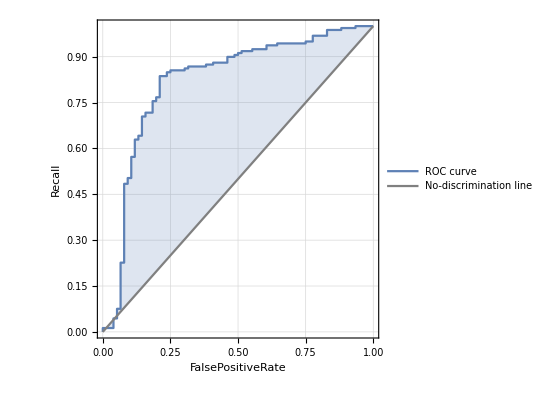
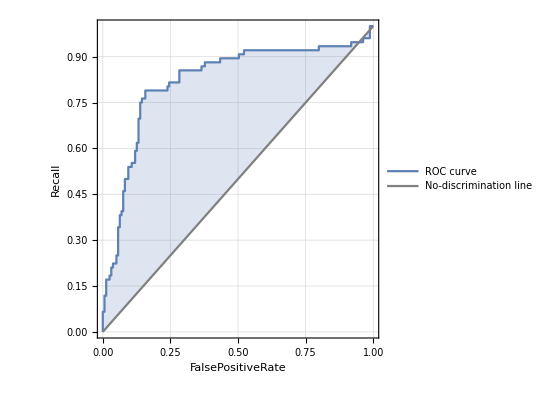
<|0→-Graphics-,1→-Graphics-|>

```mathematica
measurementslr["ROCCurve"]
```

The ROC curve for both classes are strongly up to the top left which indicates good performance. The diagonal line at 45 degrees represents a randomised classification.

### Neural Network

A neural network is inspired by the human brain’s network of neurons. Layers of nodes are weighted to discover patterns in data and create models.

#### Train the model

```mathematica
nnFun =Classify[Values[trainData,#Features&]->Values[trainData,#Objective&],Method->"NeuralNetwork"];
```

```mathematica
Information[nnFun,"MethodDescription"]
```

An neural networks is composed of layers of artificial neuron units. Each 
unit computes its value as a function of the unit values in the previous layer. Information 
is processed layer by layer from the feature layer to the output layer which gives the class probabilities. It is 
also called a feed-forward neural network or a multi-layer perceptron.

Append Test Classifications

Now I will use the trained model to classify the test set, and append the classification results as a new column .

```mathematica
featSplit=tt[{"Test"->Query[All,Append[#,<|"Classified as"->nnFun@#Features|>]&]}];
```

Now each example contains:

```mathematica
featSplit["Test",5]
```

#### Classifier Evaluation

```mathematica
ClassifierInformation[nnFun]
```

Classifier information
Data type | {Numerical,Boolean,Numerical}
Classes | ,,01
Accuracy | (77.62.1) %
Method | NeuralNetwork
Single evaluation time | 3.66 ms/example
Batch evaluation speed | 57.8 examples/ms
Loss | 0.521 ± 0.025
Model memory | 429. kB
Training examples used | 941 examples
Training time | 14.2 s
 |

The model used 4322 examples which is 80% of the data for training. The data types of the model features are
 Numerical, Boolean, Boolean. Age is numerical and sex and chronic disease binary are booleans.

In order to evaluate the model I will create a classifier measurements object and access a number of the available classifier measurements.

The classifier measurements I will use here are :

Accuracy : The classification accuracy of the classifier. This is the fraction of classifications which are correct.

Error : The error rate of the classifier. Accuracy + Error = 1.

Precision : This is the proportion of positive classifications which are correct.

Recall : This is the true positive rate.

F1 Score : provides an average measure of recall and precision. A measure of models accuracy.

```mathematica
measurementsNN=ClassifierMeasurements[nnFun,Values[testData,#Features&]->Values[testData,#Objective&]];
nnRes = Labeled[TextGrid[{{"Accuracy","Error","Precision","Recall","F1Score"},{ measurementsNN["Accuracy"], measurementsNN["Error"], measurementsNN["Precision"], measurementsNN["Recall"], measurementsNN["F1Score"]}},Frame->All],"Neural Network Classifier Measures",Top]
```

Accuracy | Error | Precision | Recall | F1Score
0.770213 | 0.229787 | <|0→0.790055,1→0.703704|> | <|0→0.899371,1→0.5|> | <|0→0.841176,1→0.584615|>Neural Network Classifier Measures

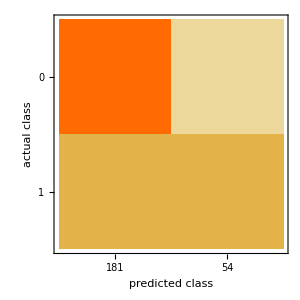
Classifier Measurements
Number of test examples | 235
Accuracy | (77.02.8) %
Accuracy baseline | (67.73.1) %
Geometric mean of probabilities | 0.615 ± 0.027
Mean cross entropy | 0.486 ± 0.043
Single evaluation time | 4.27 ms/example
Batch evaluation speed | 27.9 examples/ms
Rejection rate | 0 %
-Graphics- |

```mathematica
measurementsNN["Report"]
```

The confusion matrix shows that 179 of the 289 examples which were of class 1 were predicted as class 0. This might be due to the fact there there is a large imbalance in the data and not many examples of class 1.

```mathematica
measurementsKNN["ROCCurve"]
```

<|0→-Graphics-,1→-Graphics-|>

The ROC curve for both classes are strongly up to the top left which indicates good performance. The diagonal line at 45 degrees represent a randomised classification.

### Model Comparison

All three models have been trained and used to classify the test set. Now I will compare the performance statistics of the three models to
determine which model performed best out of the three models.

#### Nearest Neighbour Results

```mathematica
knnRes
```

Accuracy | Error | Precision | Recall | F1Score
0.778723 | 0.221277 | <|0→0.809249,1→0.693548|> | <|0→0.880503,1→0.565789|> | <|0→0.843373,1→0.623188|>Nearest Neighbour Classifier Measures

```mathematica
Logistic Regression Results
```

Logistic Regression Results

```mathematica
lrRes
```

Accuracy | Error | Precision | Recall | F1Score
0.782979 | 0.217021 | <|0→0.803371,1→0.719298|> | <|0→0.899371,1→0.539474|> | <|0→0.848665,1→0.616541|>Logistic Regression Measures

#### Neural Network Results

```mathematica
nnRes
```

Accuracy | Error | Precision | Recall | F1Score
0.770213 | 0.229787 | <|0→0.790055,1→0.703704|> | <|0→0.899371,1→0.5|> | <|0→0.841176,1→0.584615|>Neural Network Classifier Measures

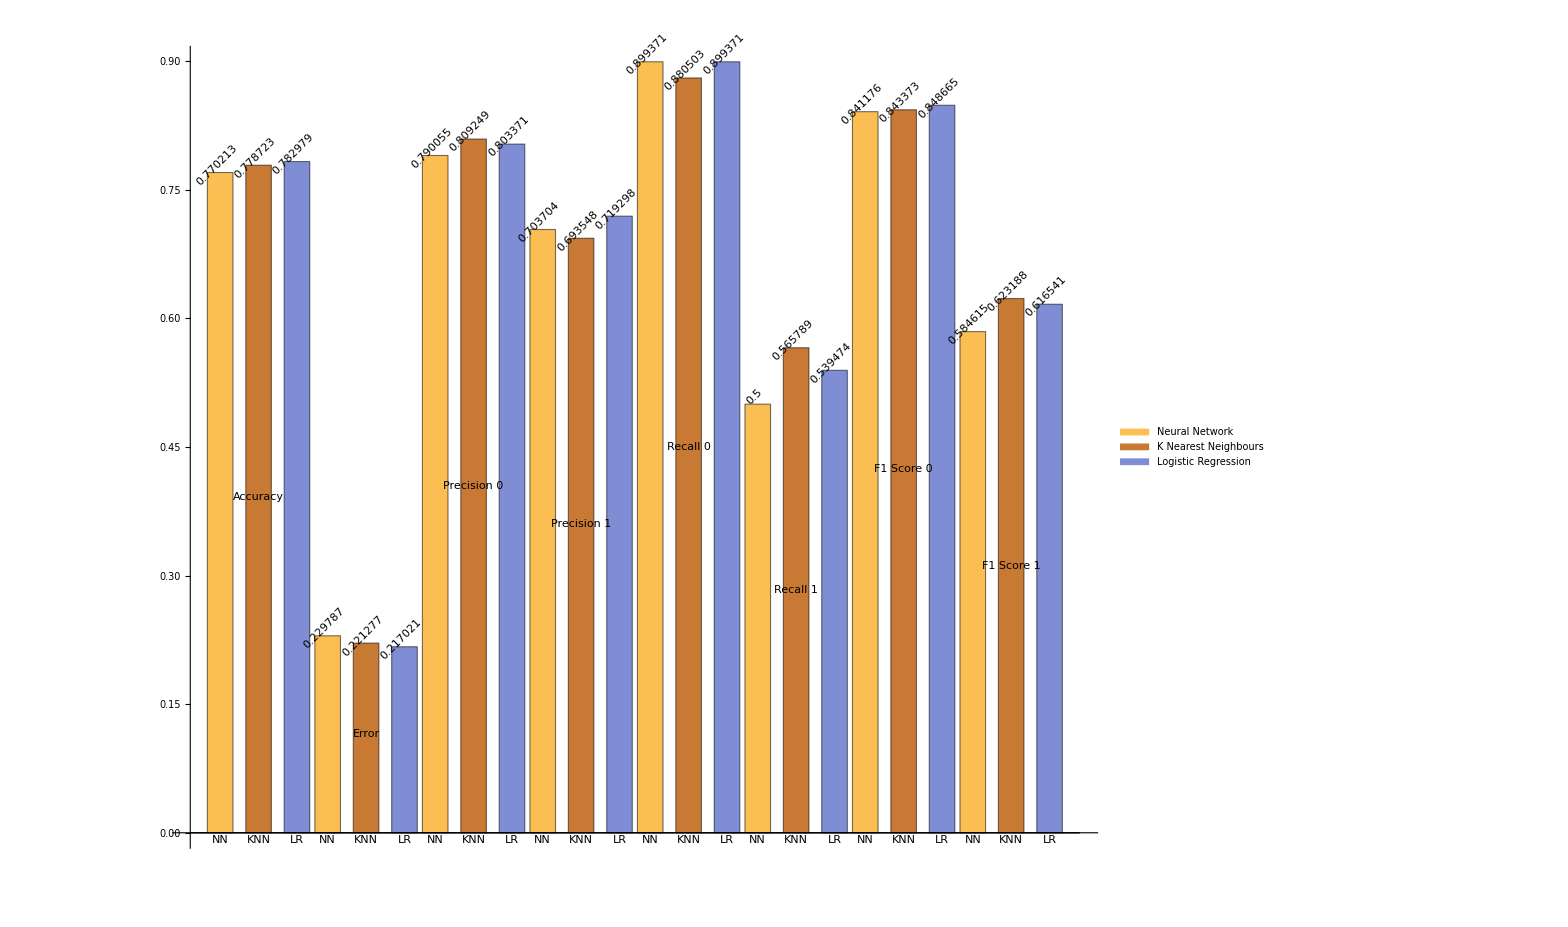

```mathematica
BarChart[Transpose[{
{measurementsNN["Accuracy"], measurementsNN["Error"], measurementsNN["Precision"][0],measurementsNN["Precision"][1], measurementsNN["Recall"][0],measurementsNN["Recall"][1], measurementsNN["F1Score"][0], measurementsNN["F1Score"][1]},
{measurementsKNN["Accuracy"], measurementsKNN["Error"], measurementsKNN["Precision"][0],measurementsKNN["Precision"][1], measurementsKNN["Recall"][0],measurementsKNN["Recall"][1], measurementsKNN["F1Score"][0], measurementsKNN["F1Score"][1]},
{measurementslr["Accuracy"], measurementslr["Error"], measurementslr["Precision"][0],measurementslr["Precision"][1], measurementslr["Recall"][0],measurementslr["Recall"][1], measurementslr["F1Score"][0], measurementslr["F1Score"][1]}}],LabelingFunction->(Placed[#,Above,Rotate[#,Pi/4]&]&),ChartLabels->{Placed[{"Accuracy","Error","Precision 0","Precision 1","Recall 0","Recall 1","F1 Score 0","F1 Score 1"},Center],{"NN","KNN","LR"}},ChartLegends->{"Neural Network","K Nearest Neighbours","Logistic Regression"},BarSpacing->Large,ImageSize->{1500,500}]
```

The accuracy was very similarly across all classifiers. The nearest neighbour classifier has the highest accuracy at 0.79371.
   In Precision the neural network is highest for the class = 0  and knn is highest for the class = 1.
     In Recall knn is highest for class = 0 and neural network is significantly highest for class = 1 .
       For F1 score the knn classifier is slightly higher than the neural net.  For class = 1 the neural network is significantly highest at 0.484988.
       F1 score is a good overall measure here and would indicate that the neural network performed best under these evaluation metrics.

## Visualisations

### Calculator

People who are highly vulnerable to covid 19 and have underlying conditions  are labeled as at risk. These people were at times advised to stay home and isolate.
A useful tool would be a risk calculator where people could input their information and be given a calculation of their level of vulnerability to the virus, 
and they would know whether or not they should isolate. The model I have trained predicts binary outcomes but with better data including accurate outcome 
values and consistent lists of symptoms and chronic diseases, a much more comprehensive calculator could be created similarly to this.

```mathematica
Labeled[DynamicModule[{fun=nnFun},Deploy[Style[Panel[Grid[Transpose[{{Style["Enter your age : "],Style["Enter your sex (1=MALE, 0=FEMALE) "],Style["Do you have any chronic disease?(0=NO,1=YES) "],Style["At Risk (0=NO,1=YES) :",Red]},{InputField[Dynamic[a],Number],InputField[Dynamic[b],Number],InputField[Dynamic[c],Number],InputField[Dynamic[fun[{a,b,c}]],Enabled->False]}}],Alignment->Right],ImageMargins->10],DefaultOptions->{InputField->{ContinuousAction->True,FieldSize->{{5,30},{1,Infinity}}}}]]],"Covid-19 At Risk Calculator"]
```

Covid-19 At Risk Calculator

### Cases Map

In  the dataset there are latitude and longitude coordinates for each case. This is an interactive map of the cases in the dataset. 
The dataset is 2.6 million records and when it is all used here the load time is extremely long. For this reason this map displays
1000 cases currently but can scale.

First pair the latitude and longitude values from the two columns :

```mathematica
samp =RandomSample[testset,10000];
```

```mathematica
l1 = Normal[samp[All,"longitude"]];
```

```mathematica
l2 = Normal[samp[All,"latitude"]];
llpairs = Transpose[{l1,l2}];
```

```mathematica
latlongF[{lat_,lon_}]:=r {Cos[lon °] Cos[lat °],Sin[lon °] Cos[lat °],Sin[lat °]};
```

```mathematica
r=6367.5;places=CountryData["Countries"];
Graphics3D[{Opacity[.8],Sphere[{0,0,0},r],Map[Line[Map[latlongF,CountryData[#,"SchematicCoordinates"],{-2}]]&,places],{Red,PointSize[Medium],Point[latlongF[#]]&/@llpairs}},Boxed->False,SphericalRegion->True,ViewAngle->0.3]
```

-Graphics3D-

### Travel History

Due to Covid - 19 travel has come to a halt. This is for obvious reason being that travel can enable the spread of the virus and also because exposure to large
 numbers of people increases the chances of becoming infected. For this reason contact tracing has been explored for its potential uses in reducing the spread of the virus.
 
 The column travel_history location contains a list of the places that the case had travelled to.

```mathematica
hist = testset[Select[#"travel_history_location"≠""&],All];
```

```mathematica
hist1 = RandomSample[hist,1000];
```

Each person’s list of travel history locations can be seen as a path. These are all of the 772 different paths that were taken:

```mathematica
GroupBy[hist,"travel_history_location",Length]
```

By splitting each route on the “;” that separates each point on the route, I get a commma separated list of the points on the route:

By entering the ID of the person who’s travel history is needed this map updates to show the places they have traveled to.

```mathematica
Manipulate[GeoListPlot[Map[ FindGeoLocation,StringSplit[hist1[p,"travel_history_location"],";"]], Joined -> True],{p,1},ControlType->InputField]
```

## Conclusions

In this section I will briefly discuss the project in retrospect.

A factor that limited this project and limits any analyses of covid-19 patient level data is the lack of availability of the data. Covid-19
is a new virus, with a short data collection period. Privacy of individuals is also a concern in today’s world and this also limits public availability
of patient level data. All data used in this project was anonymized and so there are no related privacy concerns. within this dataset there was a 
lot of missing or inconsistent data which again limited the model training. 

A significant improvement to the model’s complexity would come from availability of patient’s chronic diseases as well as symptoms. This would also
improve the effectiveness of the Covid-19 Risk calculator.

The Neural Network Classifier outperformed the Nearest Neighbour and the Logistic Regression Classifiers on this sample.

There are many useful visualisations and tools to be created from patient level data that can be used for a wide variety of tasks
as shown in the visualisations section of this project.